### Drawing edges between gaussian primes Strategy: generate a list of the Gaussian primes in the area from the x-axis to the line y = x. Because of the area we’ve limited ourselves to, we’ll only need to calculate one Gaussian prime per prime number. For each gaussian prime, determine the neighboring gaussian primes that are at most distance k away. Reflect the adjacent points across the line y = x, the x-axis and the y-axis to generate the list of all adjacent points in the graph. Draw the lines. Draw all gaussian primes. Let k be the maximum distance (or length) of an edge between 2 Gaussian points Let S be the set of all possible points of distance less than or equal to k from the origin (or norm less than or equal to k^2) in Q1 Let m be the maximum distance from the origin that we want to explore Let V be the set of Gaussian primes in Q1 between the x-axis and the line y=x of at most distance m from the origin Let L be the list of edges between g-primes of distance <= k For each member, v, of V, add v to each member, s, of S. if v+s is a g-prime, add {v, v+s} to L Reflect each member of L across y=x, then across the y=axis into Q2, then across x-axis into Q3 and Q4 Draw the lines

Let S be the set of all possible points of distance less than or equal to k from the origin (or norm less than or equal to k^2) in Q1

```mathematica
positiveKPoints[max_] := Select[Tuples[Range[0,max], 2], (#[[1]] > 0 && #[[1]] >= #[[2]]) &]
negativeKPoints[max_] := Map[{#[[1]], -#[[2]]}&, positivekPoints[max]]
generateKPoints[max_] := Union[positivekPoints[max], negativekPoints[max]]
```

### Let V be the set of Gaussian primes in Q1 between the x-axis and the line y=x of at most distance m from the origin

```mathematica
(*PowersRepresentation returns values in ascending order, need to reverse the values so they stay between x-axis and y=x*)
mod1Point[p_] :=Flatten[Reverse/@PowersRepresentations[p,2,2]]
mod3Point[p_] := Return[{p,0}]
```

### Call the appropriate function depending on congruence of p mod 4

```mathematica
generatePrimePoint[p_, maxXDistance_, primeList_] := 
Which[Mod[p,4] == 1 && p ≤ 2(maxXDistance)^2,Append[primeList, mod1Point[p]], p ≤ maxXDistance, Append[primeList,mod3Point[p]],True, primeList]
```

### Generate all primes up to a maximum point on the x axis. Add {1,1} to the list to make up for 2 being missed by the congruence rules

```mathematica
generatePrimeList[currentPrimeIndex_, stopPrimeIndex_, maxXDistance_, primeList_] := 
If[currentPrimeIndex > stopPrimeIndex, primeList, generatePrimeList[currentPrimeIndex + 1, stopPrimeIndex, maxXDistance, generatePrimePoint[Prime[currentPrimeIndex], maxXDistance, primeList]]]
```

### For each member, v, of V, add v to each member, s, of S. if v+s is a g-prime, add {v, v+s} to L

```mathematica
(*Add each member of s to v, return the points that are gaussian primes *)
getPrimePoints[v_,sList_] := Select[Map[v+#&, sList], PrimeQ[#[[1]] + #[[2]] I ] &]

(*For each adjacent point to v that is gaussian point, append v and the adjacent point to the line list*)
getPrimeEdges[v_, primeNeighbors_, edgeList_] := 
If[Length[primeNeighbors]  > 0, getPrimeEdges[v, Drop[primeNeighbors, 1], Append[edgeList, {v, primeNeighbors[[1]]} ]], edgeList]

(*generate the list of all edges in the graph*)
generateEdgeList[primeList_, sList_, edgeList_] :=
If[Length[primeList] ≠ 0, generateEdgeList[Drop[primeList, 1], sList, getPrimeEdges[primeList[[1]], getPrimePoints[primeList[[1]], sList], edgeList]], edgeList]
```

{{1,-1},{1,0},{1,1}}

{{1,1},{3,0},{2,1},{7,0},{3,2},{4,1},{5,2},{6,1},{5,4},{7,2},{6,5},{8,3},{8,5},{9,4},{10,1},{10,3},{8,7},{11,4},{10,7},{11,6},{13,2},{10,9},{12,7},{14,1}}

{{2,0},{2,1}}

{{{1,1},{2,0}},{{1,1},{2,1}}}

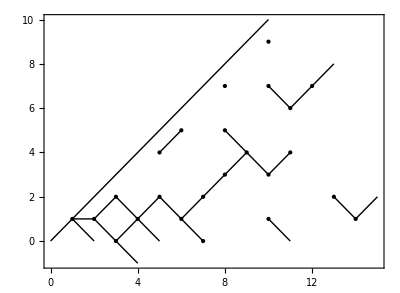

```mathematica
kMax = 1;
s = generateKPoints[kMax]
pt = {1,1};
maxDistance = 10;
v = generatePrimeList[2, PrimePi[2*maxDistance^2], maxDistance, {{1,1}}]
getPrimePoints[pt, s]
getPrimeEdges[pt, getPrimePoints[pt, s], {}]
edgeList = generateEdgeList[v, s, {}];
Graphics[{Line[edgeList], Point[v], Line[{{0,0}, {10,10}}]}, Frame->True, FrameTicks->Automatic]
```